{{﻿Time,Displacement Z Node 48},{0,0},{0.01,-1.56×10^-26},{0.02,-1.41×10^-25},{0.03,-2.29×10^-25},{0.04,5.06×10^-25},{0.05,1.83×10^-24},{0.06,3.2×10^-24},{0.07,-9.01×10^-25},{0.08,-2.64×10^-23},{0.09,-9.17×10^-23},{0.1,-2.12×10^-22},{0.11,-3.98×10^-22},27974,{279.86,-0.00350529},{279.87,-0.00354085},{279.88,-0.00353144},{279.89,-0.00347712},{279.9,-0.00337835},{279.91,-0.00323618},{279.92,-0.00305245},{279.93,-0.00282975},{279.94,-0.0025714},{279.95,-0.00228118},{279.96,-0.00196314},{279.97,-0.00162126},{279.98,-0.00125922}}
 |  |  |  |

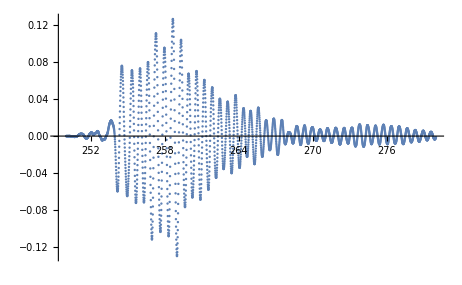

3001

```mathematica
ClearAll["Global`*"];
data=Import[FileNameJoin[{NotebookDirectory[],"model300_disp.csv"}],"Data"]
(*Convert scientific notation strings to numbers*)
(*意味のあるデータは25000辺りからですね*)
time=data[[25000;;,1]];
disp=data[[25000;;,2]];
ListPlot[Transpose[{time,disp}],PlotRange->All]
Length[time]
```

```mathematica
(*これはテストケースです．*)
(*time=Table[t,{t,200,300,0.1}];
T=10.;
disp=Table[Sin[2π/T*t],{t,200,300,0.1}];
ListPlot[Transpose[{time,disp}],PlotRange->All]*)
```

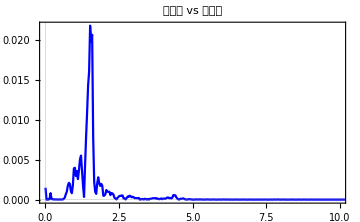

Power::infy: 無限式1/0が見付かりました．

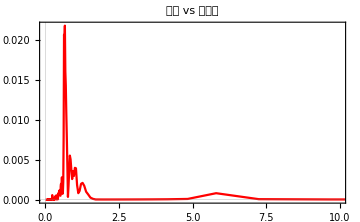

```mathematica
(*Recreate*)
n=5000;
tstart=250;
tend=279;
c=2/Sqrt[n];
tmp=Interpolation[Transpose[{time,disp}]];

interpdata=Table[{t,tmp[t]},{t,Subdivide[tstart,tend,n-1]}];

fft=c*Abs[Fourier[interpdata[[;;-1,2]]]];
Fs=n/(tend-tstart);
freq=Table[i*Fs/n,{i,0,n/2-1}];

ListPlot[Transpose[{freq,fft[[;;n/2]]}],
Joined->True,
PlotStyle->Blue,
PlotRange->{{0,10},All},
ImageSize->Medium,
PlotLabel->"周波数 vs 加速度",
PlotTheme->"Scientific"]

ListPlot[Transpose[{1/freq,fft[[;;n/2]]}],
Joined->True,
PlotStyle->Red,
PlotRange->{{0,10},All},
ImageSize->Medium,
PlotLabel->"周期 vs 加速度",
PlotTheme->"Scientific"]
```

```mathematica
max=Max[fft[[;;n/2]]]
index=firstMaxIndex=Position[fft[[;;n/2]],max][[1]]
N[freq[[index]]]
```

0.0217685

{45}

{1.51724}

```mathematica
freqVSfft=Transpose[{N[freq],fft[[;;n/2]]}];
Export[FileNameJoin[{NotebookDirectory[],"result.csv"}],freqVSfft]
```

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_Fourier/result.csv